```mathematica
Int[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅇ^(ⅈ p x-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(500 λ))/.λ->π/2,{p,-10^range,10^range},MaxRecursion->50(*,WorkingPrecision->30,PrecisionGoal->15*)]
DInt[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅈ ⅇ^(ⅈ p x-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(500 λ)) p/.λ->π/2,{p,-10^range,10^range},MaxRecursion->50(*,WorkingPrecision->30,PrecisionGoal->15*)]
```

```mathematica
Table[Re[e/.FindRoot[Int[e,0]==0,{e,#}]],{range,1,5,0.5}]&/@{2,3.5,5}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -9.62078×10^-15+2.22045×10^-16 ⅈ 和 4.78001×10^-15.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.44058×10^-13+8.00835×10^-15 ⅈ 和 5.30317×10^-14.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.44058×10^-13+8.00835×10^-15 ⅈ 和 5.30317×10^-14.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{{1.85052,1.83395,1.83398,1.83398,1.83398,1.83398,1.83398,1.83398,2.},{3.32526,3.30912,3.30908,3.30908,3.30908,3.30908,3.30908,3.30908,3.5},{4.78123,4.79169,4.79172,4.79172,4.79172,4.79172,4.79172,4.79172,5.}}

```mathematica
Block[{range=2},Re[e/.FindRoot[Int[e,0]==0,{e,#}]]&/@{2,3.5,5}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.24125×10^-13+3.44343×10^-16 ⅈ 和 5.64983×10^-14.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.24125×10^-13+3.44343×10^-16 ⅈ 和 5.64983×10^-14.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -4.15987×10^-15+2.92821×10^-15 ⅈ 和 5.31387×10^-14.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{1.83398,3.30908,4.79172}

```mathematica
Block[{range=2},Re[e/.FindRoot[Int[e,0]==0,{e,2.9,3.2}]]]
```

NIntegrate::precw: 参数函数的精度 (ⅇ^(-(ⅈ (1450. p-(100 p^3)/3+p^5/5))/(250 π))) 小于 WorkingPrecision (30.).

NIntegrate::precw: 参数函数的精度 (ⅇ^(-(ⅈ (1600. p-(100 p^3)/3+p^5/5))/(250 π))) 小于 WorkingPrecision (30.).

NIntegrate::precw: 参数函数的精度 (ⅇ^(-(ⅈ (1450. p-(100 p^3)/3+p^5/5))/(250 π))) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NIntegrate::precw 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -8.9697182359334925552466174679×10^-10-1.46586509442247056924584318059×10^-9 ⅈ 和 0.0120747184096584600681347160435.

3.30908

```mathematica
Table[Re[e/.FindRoot[DInt[e,0]==0,{e,#}]],{range,1,5,0.5}]&/@{0.5,3,4}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 4.82947×10^-15+3.42434×10^-15 ⅈ 和 2.59381×10^-14.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.72175×10^-8+1.66013×10^-11 ⅈ 和 1.03511×10^-12.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{{0.616773,0.591354,0.59114,0.591132,0.591132,0.591132,0.591132,0.591132,0.591132},{3.08346,3.05241,3.0525,3.0525,3.0525,3.0525,3.0525,3.0525,3.0525},{6.55762,3.05241,3.0525,3.0525,3.0525,3.0525,3.0525,3.0525,3.0525}}

```mathematica
Block[{range=5,re},re=Re[e/.FindRoot[DInt[e,0]==0,{e,2.2,2.5}]];{re,Int[re,10^7]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.91941×10^-11-7.49401×10^-16 ⅈ and 7.53707×10^-13 for the integral and error estimates.

{2.18272,0.0136693-4.57861×10^-14 ⅈ}

```mathematica
Block[{range=5},Int[2.1827176195388387,10^10]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000583157+2.96965×10^-8 ⅈ and 9.95188×10^-10 for the integral and error estimates.

0.000583157+2.96965×10^-8 ⅈ

```mathematica
Block[{range=3},Plot[Int[3.0525,x],{x,10,10^2}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

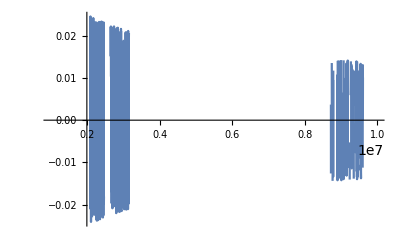

```mathematica
Block[{range=3},Plot[Int[3.0525,x],{x,10^6,10^7}]]
```

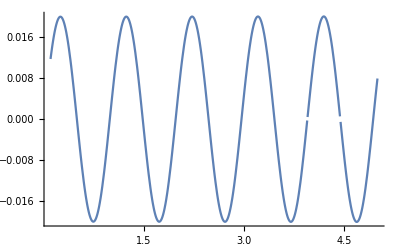

```mathematica
Plot[Block[{range=1},DInt[e,1000]],{e,0.1,5}]
```

```mathematica
Plot[Block[{range=3},DInt[e,500]],{e,0.1,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

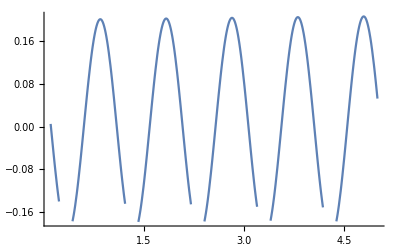

```mathematica
Plot[Block[{range=1},DInt[e,100]],{e,0.1,5}]
```

```mathematica
Block[{range=2},Re[e/.FindRoot[DInt[e,0]==0,{e,2.2,2.5}]]]
```

NIntegrate::precw: 参数函数的精度 (ⅈ ⅇ^(-(ⅈ (1100. p-(100 p^3)/3+p^5/5))/(250 π)) p) 小于 WorkingPrecision (30.).

NIntegrate::precw: 参数函数的精度 (ⅈ ⅇ^(-(ⅈ (1250. p-(100 p^3)/3+p^5/5))/(250 π)) p) 小于 WorkingPrecision (30.).

NIntegrate::precw: 参数函数的精度 (ⅈ ⅇ^(-(ⅈ (1100. p-(100 p^3)/3+p^5/5))/(250 π)) p) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NIntegrate::precw 的进一步输出将被抑制.

2.18272

NIntegrate::precw: 参数函数的精度 (ⅈ ⅇ^(-(ⅈ (1520. p-(100 p^3)/3+p^5/5))/(250 π)) p) 小于 WorkingPrecision (30.).

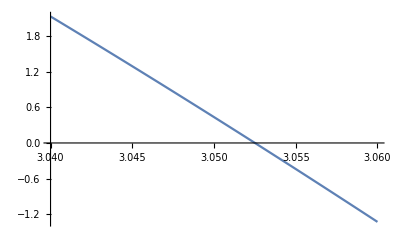

```mathematica
Plot[Block[{range=3},DInt[e,0]],{e,3.04,3.06}]
```

NIntegrate::precw: 参数函数的精度 (ⅈ ⅇ^(-(ⅈ (50.0501 p-(100 p^3)/3+p^5/5))/(250 π)) p) 小于 WorkingPrecision (30.).

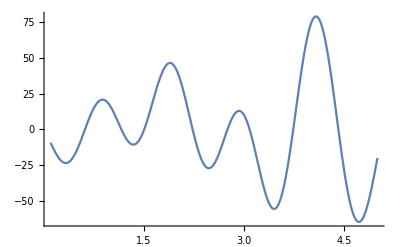

```mathematica
Plot[Block[{range=1},DInt[e,0]],{e,0.1,5}]
```

NIntegrate::precw: 参数函数的精度 (ⅇ^(-(ⅈ (50.0501 p-(100 p^3)/3+p^5/5))/(250 π))) 小于 WorkingPrecision (30.).

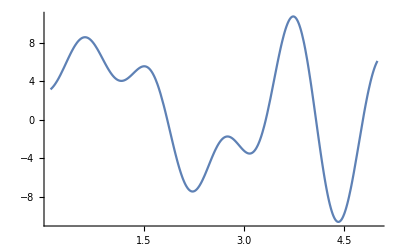

```mathematica
Plot[Block[{range=1},Int[e,0]],{e,0.1,5}]
```

```mathematica
(*μ=25*)
Int[e_?Reals,x_?NumberQ]:=NIntegrate[ⅇ^(-(ⅈ (500000 e p-(10000 p^3)/3+p^5/5))/(250000 π)+ⅈ p x),{p,-range,range},MaxRecursion->30,WorkingPrecision->30,PrecisionGoal->15]
DInt[e_?Reals,x_?NumberQ]:=NIntegrate[ⅈ ⅇ^(-(ⅈ (500000 e p-(10000 p^3)/3+p^5/5))/(250000 π)+ⅈ p x) p,{p,-range,range},MaxRecursion->30,WorkingPrecision->30,PrecisionGoal->15,Method->"Trapezoidal"]
```

```mathematica
Block[{range=100},Re[e/.FindRoot[Int[e,0]==0,{e,0.7,0.85}]]]
```

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (350000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (425000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (350000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

0.834191

```mathematica
Block[{range=100},Re[e/.FindRoot[Int[e,0]==0,{e,1.4,1.5}]]]
```

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (700000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (750000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (700000. p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

1.47727

```mathematica
Block[{range=100},Re[e/.FindRoot[DInt[e,0]==0,{e,0.36,0.38}]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (180000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (190000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (180000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

0.352774

```mathematica
Block[{range=100},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.17,1.18},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (585000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -199.482453805191647150148131876+0.841281380364144658237433213398 ⅈ and 2.83109052092885767725470520849 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (590000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -166.109280150446978770856824215-1.16644053997133545633307560231 ⅈ and 2.83373600762834857042256343056 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (585000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -200.573294765123391308871512589-1.54737000003157981903124416903 ⅈ and 2.83193629480766722677077097583 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.2282

1.20391

1.2039

1.20383

1.20419

1.20524

1.19159

1.19169

1.19245

1.19827

1.19827

1.19826

1.19824

1.19857

1.19689

1.1953

1.19532

1.19532

1.19533

1.19532

1.19528

1.19542

$Aborted

```mathematica
Block[{range=500},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.16,1.18},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (580000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 83.7488643337754227680586743016+416.298468903055586241454401141 ⅈ and 94.9700729281633139753609688874 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (590000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -27.7666180401371084805941032492+212.018311464843294014508919976 ⅈ and 95.0600215951924659906752995379 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (580000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -752.591319965645274433791251682-43.7223317562761558102799389865 ⅈ and 94.7121838665835256040415925464 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.17885

1.18011

1.17955

1.18105

1.17983

1.17966

1.17956

1.17955

1.17955

1.17955

«16 more identical outputs»

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

1.17955

```mathematica
Block[{range=1000},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.16,1.18},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (580000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -254.177349565291815117450257011+848.524561747391577308720450515 ⅈ and 380.657374217706254131126979928 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (590000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2225.63918372320985153713239474-1007.34563209474619701505394248 ⅈ and 378.186958173503919217826613354 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (580000. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 110.686748465735046264863809381-1451.80192105871498361713060188 ⅈ and 373.772596626081886793660764684 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.1632

1.16306

1.16077

1.16266

1.16304

1.16304

1.16304

«13 more identical outputs»

$Aborted

```mathematica
Block[{range=1500},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.165,1.179},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (582500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -835.016324549995088126412816173-1190.48506867941016730483590341 ⅈ and 844.998586877341074033952342537 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (589500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 679.505773310814153663843475369-3504.36940246939552889726422365 ⅈ and 852.483885070187577082090186867 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (582500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4886.35051447414404177270217246+16.7995025247980419059016432055 ⅈ and 849.087695896616169932576106959 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.17894

1.17891

1.17895

1.17895

1.17895

1.17894

1.17894

1.17894

«4 more identical outputs»

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.17894

```mathematica
Block[{range=500},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.165,1.175},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (582500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -79.640467911924357078079300053-48.1297935364944866954317689087 ⅈ and 95.8540069172847147365618718811 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (587500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -403.494491191260303781242130406-352.092183948447919092209213403 ⅈ and 94.399560970560114600325794797 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (582500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -454.865797598577932166179189543-262.973582798563049787503663438 ⅈ and 94.8721477428850714645931863421 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.16493

1.16489

1.16459

1.16488

1.16488

1.16489

1.16488

1.16488

1.16488

1.16489

1.16488

1.16488

1.16488

«10 more identical outputs»

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

1.16488

```mathematica
Block[{range=500},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.167,1.173},StepMonitor:>Print[Re[e]]]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (583500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -427.906588618464447299723376039-238.16191189684790535997445261 ⅈ and 95.4514916553236970604994937277 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (586500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -548.217887771799499385093093407+405.39763066882145954949686576 ⅈ and 95.9806505932894588744864885581 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (583500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -264.275544744402412804328426547-196.790583218405255217017976505 ⅈ and 95.0482595534307264909894682846 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.16703

1.1671

1.1671

1.1671

«11 more identical outputs»

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

1.1671

```mathematica
Block[{range=1000},Re[e/.FindRoot[DInt[Re[e],0]==0,{e,1.167,1.173},StepMonitor:>Print[Re[e]],WorkingPrecision->30,PrecisionGoal->10]]]
```

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (583500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 316.267878730079339357035733053+227.693242573434625196361424377 ⅈ and 378.69347944540200205814623499 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (586500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -409.687027106428547189665709406-635.265415263850985506509131773 ⅈ and 380.580103740212530694440735756 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (ⅈ ⅇ^(-(ⅈ (583500. p-(10000 p^3)/3+p^5/5))/(250000 π)) p) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 743.739407958552411401962184425-249.531586789998864250002953937 ⅈ and 376.393624452687158811593939286 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

1.1729999999998473258936436825

1.17299999999984732589048867978

1.17299999999984732589273723688

1.17299999999984732589053320819

1.17299999999984732589071497831

1.17299999999984732589055922922

1.17299999999984732589053442986

1.17299999999984732589053281552

1.17299999999984732589053325461

1.17299999999984732589053319189

1.17299999999984732589053320645

1.1729999999998473258905332084

1.17299999999984732589053320826

1.17299999999984732589053320809

1.17299999999984732589053320818

1.17299999999984732589053320819

1.17299999999984732589053320819

1.17299999999984732589053320819

FindRoot::frdig: 30. working digits is insufficient to achieve the absolute tolerance 1.×10^-15.

1.17299999999984732589053320819